{2.03,1.78994,1.69668,1.88825,1.47359,1.67593,1.48408,1.14952,1.93519,1.88942,1.83348,2.04009,1.85316,1.53385,1.41454,1.58924,1.48822,1.46901,1.3623,1.78568,1.54261,1.35749,1.82431,1.11828,1.95564,1.19887,1.84421,1.74611,1.80243,1.48979,1.59778,1.75138,1.23122,1.57374,1.14208,1.35526,1.12434,1.58352,1.51514,1.86065,1.13279,1.28056,1.11151,1.45693,1.66418,1.39612,1.55344,1.91644,1.96257,1.40639,1.34036,1.60552,1.87378,1.82335,1.28255,1.45447,1.95523,1.3227,1.22381,1.94985,1.55488,1.9384,1.90662,1.54461,1.1069,1.74165,1.88213,1.1062,1.63602,1.60794,1.47109,1.78804,1.4018,1.10889,1.36882,1.19782,1.81961,1.71177,1.49458,1.33262,1.46082,1.46467,1.94575,1.70546,1.99493,1.41554,1.90883,1.89575,1.23308,1.48993,1.87982,1.8736,1.29682,1.18404,1.37747,1.39701,1.45606,1.19283,1.23183,1.71025}

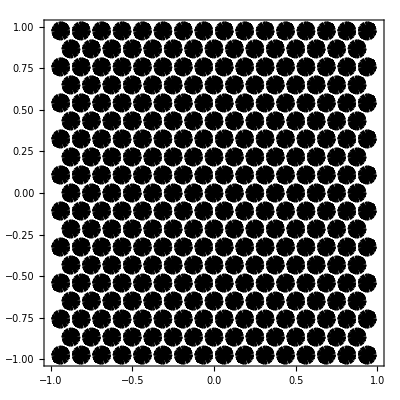

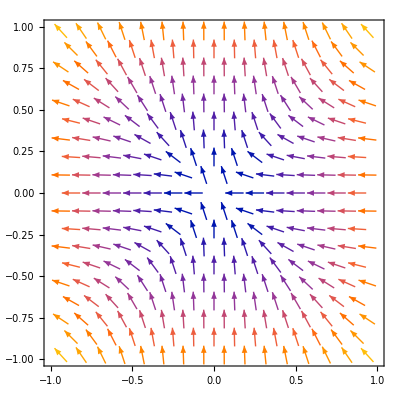

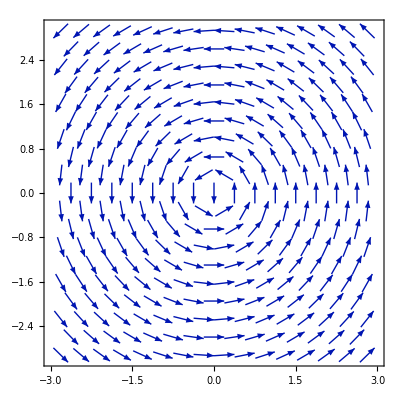

```mathematica
VectorPlot[{-x^2,y^2},{x,-1,1},{y,-1,1}]
```

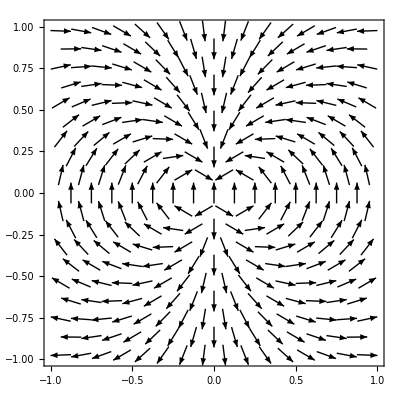

```mathematica
VectorPlot[Evaluate[TransformedField["Polar"->"Cartesian",{-Sin[θ],Cos[θ]},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1},VectorColorFunction->(Black&)]
```

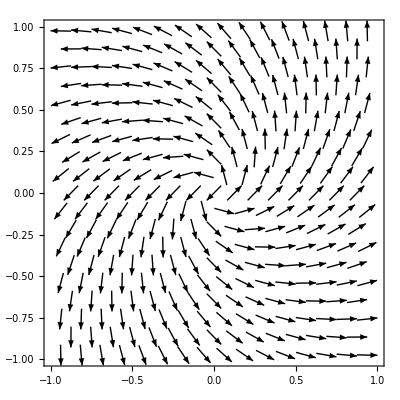

{1.75169,1.86336,2.0321,1.913,1.57421,1.59923,1.27995,1.41685,1.25384,1.48574}

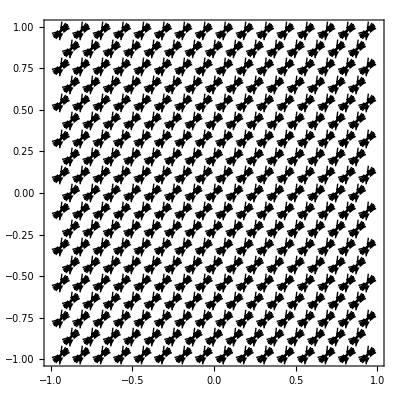

```mathematica
VectorPlot[Evaluate[TransformedField["Polar"->"Cartesian",{1,1},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1},VectorColorFunction->(Black&)]
```

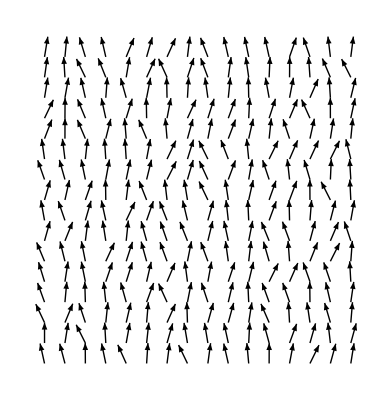

```mathematica
datain=Partition[ToExpression["{"<>StringReplace[Import["/home/jose/Documents/Maestria/thesis/chapters/figures/configurations.txt"],RegularExpression["\\s"]->","]<>"}"],4];
arrow=Map[Arrow[{Take[#,2],Take[#,2]+Drop[#,2]}]&,datain];
Graphics[{arrow}]
```